```mathematica
$Assumptions=mu>0&&m>0
RenF=(mu^2 Exp[EulerGamma]/(4 Pi))^((4-d)/2)
I0=(-1)^n I/(4 Pi)^(d/2) Gamma[n-d/2]/Gamma[n] 1/Δ^(n-d/2)
I1=(-1)^(n-1)I/(4 Pi)^(d/2) d/2 Gamma[n-d/2-1]/Gamma[n] 1/Δ^(n-d/2-1)
```

mu>0&&m>0

2^(-4+d) ⅇ^(1/2 (4-d) EulerGamma) (mu^2)^((4-d)/2) π^(1/2 (-4+d))

(ⅈ (-1)^n 2^-d π^(-d/2) Δ^(d/2-n) Gamma[-d/2+n])/Gamma[n]

(ⅈ (-1)^(-1+n) 2^(-1-d) d π^(-d/2) Δ^(1+d/2-n) Gamma[-1-d/2+n])/Gamma[n]

```mathematica
I1/I0/.d->4-2ep/.n->3//FullSimplify
```

((-2+ep) Δ)/ep

```mathematica
2
```

```mathematica
Integrate[2/(x a+y b +(1-x-y) c)^3,{x,0,1},{y,0,1-x} ,GenerateConditions->False]
Integrate[2 x/(x A+(1-x) B)^3,{x,0,1},GenerateConditions->False]
Integrate[2y/(y (x a+(1-x)b)+(1-y)c)^3,{x,0,1},{y,0,1},GenerateConditions->False]
```

1/(a b c)

1/(A^2 B)

1/(a b c)

```mathematica
Free
```

```mathematica
DFree=(x a+y b+(1-x-y) c)/.c->k^2/.a->(pe+k)^2-m^2/.b->(P+k)^2//Expand;
DFree=(y (x a+(1-x) b)+(1-y) c)/.c->k^2/.b->(pe+k)^2/.a->(P+k)^2-m^2//Expand
DFree=DFree/.pe^2->0/.P^2->m^2

DFree=DFree/.k->l-y(x P+(1-x)pe)//Expand
DFree=DFree/.P^2->m^2/.pe^2->0//FullSimplify
```

k^2+2 k pe y+pe^2 y-m^2 x y+2 k P x y+P^2 x y-2 k pe x y-pe^2 x y

k^2+2 k pe y+2 k P x y-2 k pe x y

l^2-pe^2 y^2-2 P pe x y^2+2 pe^2 x y^2-P^2 x^2 y^2+2 P pe x^2 y^2-pe^2 x^2 y^2

l^2+x (2 P pe (-1+x)-m^2 x) y^2

```mathematica
DeltaFree=-DFree/.l^2->0//FullSimplify
```

x (-2 P pe (-1+x)+m^2 x) y^2

```mathematica
I0Free=FullSimplify[I0/.n->3/.Δ-> DeltaFree,m>0&&d>0]
I0Free=RenF I0Free/.d->4-2ep//Simplify
I1Free=FullSimplify[I1/.n->3/.Δ-> DeltaFree,m>0&&d>0];
I1Free=RenF I1Free/.d->4-2 ep//Simplify;
```

-ⅈ 2^(-1-d) π^(-d/2) (x (-2 P pe (-1+x)+m^2 x) y^2)^(1/2 (-6+d)) Gamma[3-d/2]

(ⅈ ⅇ^(ep EulerGamma) mu^(2 ep) (x (-2 P pe (-1+x)+m^2 x) y^2)^-ep Gamma[1+ep])/(32 π^2 x (2 P pe (-1+x)-m^2 x) y^2)

```mathematica
Integrate[y y^n y^(2(-1-ep)),{y,0,1}]
```

ConditionalExpression[1/(-2 ep+n),2 Re[ep]<Re[n]]

```mathematica
I[1]
```

```mathematica
S1=Series[x (x (-2 P pe (-1+x)+m^2 x))^(1/2 (-6+d))/.d->4-2 ep,{ep,0,1}]
FullSimplify[Integrate[SeriesCoefficient[S1,0],{x,0,1},GenerateConditions->False]/.P->m/.pe->Ee/.Ee->xe m/2,1>xe>0&&m>0]
FullSimplify[Integrate[SeriesCoefficient[S1,1],{x,0,1},GenerateConditions->False]/.P->m/.pe->Ee/.Ee->xe m/2,1>xe>0&&m>0]/.PolyLog[2,(-1+xe)/xe]->PolyLog[2,xe]-Log[xe]^2/2+Log[1-xe] Log[xe]-Pi^2/6//Simplify
```

1/(-2 P pe (-1+x)+m^2 x)-(Log[x (-2 P pe (-1+x)+m^2 x)] ep)/(-2 P pe (-1+x)+m^2 x)+O[ep]^2

Log[xe]/(m^2 (-1+xe))

-(π^2+12 Log[m] Log[xe]-6 Log[1-xe] Log[xe]+6 Log[xe]^2-6 PolyLog[2,xe])/(6 m^2 (-1+xe))

```mathematica
PolyLog[2,(-1+xe)/xe]==PolyLog[2,xe]-Log[xe]^2/2+Log[1-xe]Log[xe]-Pi^2/6/.xe->Pi/7//N
```

True

```mathematica
S2=Series[x^2(x (-2 P pe (-1+x)+m^2 x))^(1/2 (-6+d))/.d->4-2 ep,{ep,0,1}]
FullSimplify[Integrate[SeriesCoefficient[S2,0],{x,0,1},GenerateConditions->False]/.P->m/.pe->Ee/.Ee->xe m/2,1>xe>0&&m>0]
FullSimplify[Integrate[SeriesCoefficient[S2,1],{x,0,1},GenerateConditions->False]/.P->m/.pe->Ee/.Ee->xe m/2,1>xe>0&&m>0]/.PolyLog[2,(-1+xe)/xe]->PolyLog[2,xe]-Log[xe]^2/2+Log[1-xe] Log[xe]-Pi^2/6//Simplify
```

x/(-2 P pe (-1+x)+m^2 x)-(x Log[x (-2 P pe (-1+x)+m^2 x)] ep)/(-2 P pe (-1+x)+m^2 x)+O[ep]^2

(1-xe+xe Log[xe])/(m^2 (-1+xe)^2)

(12-12 xe-π^2 xe+6 xe Log[xe]+6 xe Log[1-xe] Log[xe]-6 xe Log[xe]^2-12 Log[m] (1-xe+xe Log[xe])+6 xe PolyLog[2,xe])/(6 m^2 (-1+xe)^2)

```mathematica
D1V1
```

```mathematica
D1V1=(x a+y b+(1-x-y) c)/.c->k^2/.a->(P+k)^2-m^2/.b->(P+k-Q)^2//Expand;
D1V1=(y (x a+(1-x) b)+(1-y) c)/.c->k^2/.b->(P+k)^2-m^2/.a->(P+k-Q)^2//Expand
D1V1=D1V1/.Q->0/.P^2->m^2
D1V1=D1V1/.k->l- y P//Expand
D1V1=D1V1/.P^2->m^2//FullSimplify
```

k^2-m^2 y+2 k P y+P^2 y+m^2 x y-2 k Q x y-2 P Q x y+Q^2 x y

k^2+2 k P y+m^2 x y

l^2+m^2 x y-P^2 y^2

l^2+m^2 (x-y) y

```mathematica
DeltaD1V1=-D1V1/.l^2->0
```

-m^2 (x-y) y

(ⅈ (-1)^n 2^-d π^(-d/2) Δ^(d/2-n) Gamma[-d/2+n])/Gamma[n]

((-1)^(-1+n) 2^(-1-d) d π^(-d/2) Δ^(1+d/2-n) Gamma[-1-d/2+n])/Gamma[n]

```mathematica
I0D1V1=FullSimplify[I0/.n->3/.Δ->DeltaD1V1,m>0&&d>0]
I1D1V1=FullSimplify[I1/.n->3/.Δ->DeltaD1V1,m>0&&d>0]
```

-ⅈ 2^(-1-d) π^(-d/2) (m^2 y (-x+y))^(1/2 (-6+d)) Gamma[3-d/2]

2^(-2-d) d π^(-d/2) (m^2 y (-x+y))^(1/2 (-4+d)) Gamma[2-d/2]

```mathematica
Ia=Integrate[(1-y)y(y (-x+y))^(1/2 (-6+d)),{x,0,y}]
Ib=Integrate[(1-y) y(y (-x+y))^(1/2 (-6+d)),{x,y,1}]
```

ConditionalExpression[-(2 (-1+y) (y^2)^(d/2))/((-4+d) y^4),Re[d]>4]

ConditionalExpression[(2 ((-1+y) y)^(1/2 (-2+d)))/((-4+d) y),Re[d]>4]

```mathematica
Iaf=Integrate[Ia[[1]],{y,0,1}]
Ibf=Integrate[Ib[[1]],{y,0,1}]
```

ConditionalExpression[2/((-4+d) (-3+d) (-2+d)),Re[d]>3]

ConditionalExpression[-(ⅈ^d 2^(3-d) √π Gamma[-1+d/2])/((-4+d) Gamma[1/2 (-1+d)]),Re[d]>2]

```mathematica
Series[Iaf[[1]]+Ibf[[1]],{d,4,0}]
```

1/2 (-3+EulerGamma-ⅈ π+2 Log[2]+PolyGamma[0,3/2])+O[d-4]^1

```mathematica
NIntegrate[(1-y) (y (-x+y))^(1/2 (-6+d))/.d->4.8,{y,0,1},{x,0,y}]
2/((-4+d)^2 (-3+d))/.d->4.8
```

1.73611

1.73611

```mathematica
NIntegrate[(1-y) (y (-x+y))^(1/2 (-6+d))/.d->4.1,{y,0,1},{x,y,1}]
-((2 I^d Gamma[-2+d/2] Gamma[d/2])/((-4+d) Gamma[-2+d]))/.d->4.1
```

-375.674-59.501 ⅈ

-375.674-59.501 ⅈ

```mathematica
Ic=Integrate[y(y (-x+y))^(1/2 (-4+d)),{x,0,y}]
Id=Integrate[y(y (-x+y))^(1/2 (-4+d)),{x,y,1}]
```

ConditionalExpression[(2 (y^2)^(-1+d/2))/(-2+d),Re[d]>2]

ConditionalExpression[-(2 ((-1+y) y)^(1/2 (-2+d)))/(-2+d),Re[d]>2]

```mathematica
Icf=Integrate[Ic[[1]],{y,0,1}]
Idf=Integrate[Id[[1]],{y,0,1}]
```

ConditionalExpression[2/((-2+d) (-1+d)),Re[d]>1]

ConditionalExpression[(ⅈ^d 2^(1-d) √π Gamma[-1+d/2])/Gamma[(1+d)/2],Re[d]>0]

```mathematica
Series[Icf[[1]]+Idf[[1]],{d,4,1}]
```

1/2+1/36 (-10-3 EulerGamma+3 ⅈ π-6 Log[2]-3 PolyGamma[0,5/2]) (d-4)+O[d-4]^2

```mathematica
D2V1
```

```mathematica
D2V1=(x a+y b+(1-x-y) c)/.c->k^2/.a->(pe+k)^2-m^2/.b->(pe+k+Q)^2//Expand
D2V1=D2V1/.Q->0/.pe^2->0
D2V1=D2V1/.k->l-(x+y)pe//Expand
D2V1=D2V1/.pe->0
```

k^2-m^2 x+2 k pe x+pe^2 x+2 k pe y+pe^2 y+2 k Q y+2 pe Q y+Q^2 y

k^2-m^2 x+2 k pe x+2 k pe y

l^2-m^2 x-pe^2 x^2-2 pe^2 x y-pe^2 y^2

l^2-m^2 x

```mathematica
I0D2V1=FullSimplify[I0/.n->3/.Δ->m^2 (x),m>0&&d>0]
I1D2V1=FullSimplify[I1/.n->3/.Δ->m^2 (x),m>0&&d>0]
```

-ⅈ 2^(-1-d) π^(-d/2) (m^2 x)^(1/2 (-6+d)) Gamma[3-d/2]

2^(-2-d) d π^(-d/2) (m^2 x)^(1/2 (-4+d)) Gamma[2-d/2]

```mathematica
I0E=Integrate[(x+y-1)x^a,{x,0,1},{y,0,1-x}]/.a->1/2(-6+d)
```

ConditionalExpression[-1/(6+11/2 (-6+d)+3/2 (-6+d)^2+1/8 (-6+d)^3),-6+Re[d]>-2]

```mathematica
I0S1=Series[I0E[[1]]/.d->4-2ep,{ep,0,2}]
```

1/(2 ep)+3/4+(7 ep)/8+(15 ep^2)/16+O[ep]^3

```mathematica
I0S2=Series[RenF 2^(-2-d) d π^(-d/2) (m^2 )^(1/2 (-4+d)) Gamma[2-d/2]/.d->4-2ep,{ep,0,1}]//FullSimplify
```

1/(16 π^2 ep)-(1+4 Log[m]-4 Log[mu])/(32 π^2)+((π^2+24 Log[m]^2+Log[m] (12-48 Log[mu])+12 Log[mu] (-1+2 Log[mu])) ep)/(192 π^2)+O[ep]^2

```mathematica
I0R=I0S1*I0S2//FullSimplify
```

1/(32 π^2 ep^2)+(1-2 Log[m]+2 Log[mu])/(32 π^2 ep)+(12+π^2+24 Log[m]^2+24 Log[mu] (1+Log[mu])-24 Log[m] (1+2 Log[mu]))/(384 π^2)+O[ep]^1

```mathematica
I1E=Integrate[ x^a,{x,0,1},{y,0,1-x}]/.a->1/2 (-4+d)
```

ConditionalExpression[1/(2+3/2 (-4+d)+1/4 (-4+d)^2),-4+Re[d]>-2]

```mathematica
I1S1=Series[I1E[[1]]/.d->4-2 ep,{ep,0,2}]
```

1/2+(3 ep)/4+(7 ep^2)/8+O[ep]^3

```mathematica
I1S2=Series[RenF(2/d-1) 2^(-2-d) d π^(-d/2) (m^2 )^(1/2 (-4+d)) Gamma[2-d/2]/.d->4-2ep,{ep,0,2}]//FullSimplify
```

-1/(32 π^2 ep)+(1+2 Log[m]-2 Log[mu])/(32 π^2)-((π^2-24 Log[mu]+24 (Log[m]+Log[m]^2-2 Log[m] Log[mu]+Log[mu]^2)) ep)/(384 π^2)+((π^2+2 Log[m/mu] (π^2+4 Log[m/mu] (3+2 Log[m/mu]))+4 Zeta[3]) ep^2)/(384 π^2)+O[ep]^3

```mathematica
I1R=I1S1*I1S2//FullSimplify
```

-1/(64 π^2 ep)-(1-4 Log[m]+4 Log[mu])/(128 π^2)-((3+π^2+24 Log[m]^2+12 Log[mu] (1+2 Log[mu])-12 Log[m] (1+4 Log[mu])) ep)/(768 π^2)+O[ep]^2

```mathematica
5/1024(128/5 I0R+192/5 I1R)//FullSimplify
```

1/(256 π^2 ep^2)+(1-8 Log[m]+8 Log[mu])/(1024 π^2 ep)+(15+2 π^2+48 Log[m]^2+12 Log[mu] (1+4 Log[mu])-12 Log[m] (1+8 Log[mu]))/(6144 π^2)+O[ep]^1

```mathematica
48 Log[m]^2+12 Log[mu] (1+4 Log[mu])-12 Log[m] (1+8 Log[mu])//Expand//FullSimplify
```

12 (1-4 Log[m]+4 Log[mu]) Log[mu/m]

```mathematica
D2V1=(y (x a+(1-x) b)+(1-y) c)/.c->k^2/.a->(pe+k)^2-m^2/.b->(pe+k+Q)^2-me^2//Expand
D2V1=D2V1/.Q->0/.pe^2->me^2
D2V1=D2V1/.k->l-y pe//Expand
D2V1=D2V1/.pe^2->me^2//FullSimplify
```

k^2-me^2 y+2 k pe y+pe^2 y+2 k Q y+2 pe Q y+Q^2 y-m^2 x y+me^2 x y-2 k Q x y-2 pe Q x y-Q^2 x y

k^2+2 k pe y-m^2 x y+me^2 x y

l^2-m^2 x y+me^2 x y-pe^2 y^2

l^2-y (m^2 x+me^2 (-x+y))

```mathematica
DeltaD2V1=-D2V1/.l^2->0
```

y (m^2 x+me^2 (-x+y))

```mathematica
I0D2V1=I0/.n->3/.Δ->DeltaD2V1
```

-ⅈ 2^(-1-d) π^(-d/2) (y (m^2 x+me^2 (-x+y)))^(-3+d/2) Gamma[3-d/2]

```mathematica
Integrate[(y (m^2 x+me^2 (-x+y)))^(-3+d/2)y,{y,0,1}]
```

ConditionalExpression[(2 ((m-me) (m+me) x)^(d/2) Hypergeometric2F1[3-d/2,1/2 (-2+d),d/2,me^2/((-m^2+me^2) x)])/((-2+d) (m^2-me^2)^3 x^3),(Re[x]≥1+Re[(m^2 x)/me^2]||Re[x]≤Re[(m^2 x)/me^2]||x-(m^2 x)/me^2∉Reals)&&Re[d]>2&&Re[(m-me) (m+me) x]>0]

```mathematica
(2 ((m) (m) x)^(d/2) Hypergeometric2F1[3-d/2,1/2 (-2+d),d/2,me^2/((-m^2) x)])/((-2+d) (m^2)^3 x^3)/.d->4-2ep
```

```mathematica
Integrate[(2 (m^2 x)^(1/2 (4-2 ep)) Hypergeometric2F1[1/2 (2-2 ep),3+1/2 (-4+2 ep),1/2 (4-2 ep),-me^2/(m^2 x)])/((2-2 ep) m^6 x^3),{x,0,1},GenerateConditions->False]
```

ConditionalExpression[-(m^(-2 (1+ep)) (((-1+ep) (m^2/me^2)^ep)/(-1+2 ep)-Hypergeometric2F1[1-ep,ep,2-ep,-me^2/m^2]))/((-1+ep) ep),2 Re[ep]<1&&((Re[me^2]≥0&&((Im[me]≥Re[me]&&Re[me]<0&&Im[me]+Re[me]≤0)||(Re[me]>0&&Im[me]+Re[me]≥0&&Im[me]≤Re[me]))&&me≠0)||m^2+Re[me^2]<0||me^2∉Reals)]

```mathematica
Series[(m^(-2 (1+ep)) (((-1+ep) (m^2/me^2)^ep)/(-1+2 ep)-Hypergeometric2F1[1-ep,ep,2-ep,-(me^2/m^2)]))/((-1+ep) ep),{ep,0,1}]
```

(-1-Log[m^2/me^2])/m^2+((-6+4 Log[m]-4 Log[m^2/me^2]+4 Log[m] Log[m^2/me^2]-Log[m^2/me^2]^2) ep)/(2 m^2)+O[ep]^2

```mathematica
D1V2=(y (x a+(1-x) b)+(1-y) c)/.c->k^2/.a->(P-Q+k)^2-me^2/.b->(pe+k)^2-me^2//Expand
D1V2=D1V2/.Q->0/.pe^2->me^2/.P^2->m^2
D1V2=D1V2/.k->l-y pe-x y P+x y pe//Expand
D1V2=D1V2/.pe^2->me^2/. P pe->m^2/.P^2->m^2//FullSimplify
```

k^2-me^2 y+2 k pe y+pe^2 y+2 k P x y+P^2 x y-2 k pe x y-pe^2 x y-2 k Q x y-2 P Q x y+Q^2 x y

k^2+2 k pe y+m^2 x y-me^2 x y+2 k P x y-2 k pe x y

l^2+m^2 x y-me^2 x y-pe^2 y^2-2 P pe x y^2+2 pe^2 x y^2-P^2 x^2 y^2+2 P pe x^2 y^2-pe^2 x^2 y^2

l^2+y (m^2 x (1+(-2+x) y)-me^2 (x+(-1+x)^2 y))

```mathematica
DeltaD1V2=-D1V2/.l^2->0
```

-y (m^2 x (1+(-2+x) y)-me^2 (x+(-1+x)^2 y))

```mathematica
I0D1V2=I0/.n->3/.Δ->DeltaD1V2
```

-ⅈ 2^(-1-d) π^(-d/2) (-y (m^2 x (1+(-2+x) y)-me^2 (x+(-1+x)^2 y)))^(-3+d/2) Gamma[3-d/2]

```mathematica
Assuming[m>me>0&&1>y>0,Integrate[y((-y (m^2 x (1+(-2+x) y)-me^2 (x+(-1+x)^2 y)))^(-3+4/2)),{x,0,1}]]
```

ConditionalExpression[(2 (ArcTanh[√((m^2-me^2)/(m^2 (1-2 y)^2+me^2 (-1+4 y)))]-ArcTanh[(1-2 y) √((m^2-me^2)/(m^2 (1-2 y)^2+me^2 (-1+4 y)))]))/(√(-(m^2-me^2) (me^2 (1-4 y)-m^2 (1-2 y)^2))),me^2/m^2+y>1&&√((m^2 (1-2 y)^2+me^2 (-1+4 y))/(m^2-me^2))>1&&me^2+√((m^2-me^2) (m^2 (1-2 y)^2+me^2 (-1+4 y)))>m^2]

```mathematica
Series[-((2 ((-m^2+me^2) x)^(d/2) Hypergeometric2F1[3-d/2,1/2 (-2+d),d/2,2-x+me^2/(m^2 x-me^2 x)])/((-2+d) (m^2-me^2)^3 x^3))/.d->4-2ep,{ep,0,2}]//Simplify
```

Log[-1+me^2/((-m^2+me^2) x)+x]/(me^2 (-1+x)^2-m^2 (-2+x) x)-((-1+Log[(-m^2+me^2) x]) Log[-1+me^2/((-m^2+me^2) x)+x] ep)/(me^2 (-1+x)^2-m^2 (-2+x) x)+((2-2 Log[(-m^2+me^2) x]+Log[(-m^2+me^2) x]^2) Log[-1+me^2/((-m^2+me^2) x)+x] ep^2)/(2 (me^2 (-1+x)^2-m^2 (-2+x) x))+O[ep]^3

```mathematica
Integrate[Log[-1+me^2/((-m^2) x)+x]/(me^2 (-1+x)^2-m^2 (-2+x) x),{x,0,1},GenerateConditions->False]
```

$Aborted

```mathematica
Log[-1+me^2/((-m^2) x)+x]/(me^2 (-1+x)^2-m^2 (-2+x) x)/.me->0
```

-Log[-1+x]/(m^2 (-2+x) x)

```mathematica
(me^2 (-1+x)^2-m^2 (-2+x) x)//Expand
```

me^2+2 m^2 x-2 me^2 x-m^2 x^2+me^2 x^2

```mathematica
Log[-1+me^2/((-m^2) x)+x]/(me^2 (-1+x)^2-m^2 (-2+x) x)
```

Log[-1-me^2/(m^2 x)+x]/(me^2 (-1+x)^2-m^2 (-2+x) x)

```mathematica
NIntegrate[(2 (ArcTanh[Sqrt[(m^2)/(m^2 (1-2 y)^2+me^2 (-1+4 y))]]-ArcTanh[(1-2 y) Sqrt[(m^2)/(m^2 (1-2 y)^2+me^2 (-1+4 y))]]))/Sqrt[-(m^2) (me^2 (1-4 y)-m^2 (1-2 y)^2)]/.m->1/.me->0.0001,{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.499984}. NIntegrate obtained 0.516129  - 30.009\ ⅈ and 0.911301 for the integral and error estimates.

0.516129-30.009 ⅈ

```mathematica
Ex=(y (x a+(1-x) b)+(1-y) c)/.a->2pe k +k^2/.b->m^2+2 P k +k^2-me^2/.c->k^2//Expand
```

k^2+m^2 y-me^2 y+2 k P y-m^2 x y+me^2 x y-2 k P x y+2 k pe x y

```mathematica
Shift[Ex]/.pe^2->me^2/.P^2->m^2/.P pe->m^2//FullSimplify
```

l^2+y (m^2 (-1+x) (-1+y+x y)+me^2 (-1+x-x^2 y))

```mathematica
I0
```

(ⅈ (-1)^n 2^-d π^(-d/2) Δ^(d/2-n) Gamma[-d/2+n])/Gamma[n]

```mathematica
(-y (-me^2 x^2 y+m^2 (-1+x) (-1+y+x y)))^(d/2-3)/.d->4-2ep//Simplify
```

```mathematica
y(-y (-me^2 x^2 y+m^2 (-1+x) (-1+y+x y)))^(-1-ep)
```

```mathematica
Integrate[y^n (-y (-me^2 x^2 y+m^2 (-1+x) (-1+y+x y)))^(-1-ep),{y,0,1}]
```

ConditionalExpression[(m^2 (-1+x))^(-1-ep) Gamma[-ep+n] Hypergeometric2F1Regularized[1+ep,-ep+n,1-ep+n,(-me^2 x^2+m^2 (-1+x^2))/(m^2 (-1+x))],Re[ep]<Re[n]&&(m^2 Re[(-1+x)/(-me^2 x^2+m^2 (-1+x^2))]≥1||Re[(-1+x)/(-me^2 x^2+m^2 (-1+x^2))]≤0||(-1+x)/(-me^2 x^2+m^2 (-1+x^2))∉Reals)&&Re[x]>1]

```mathematica
Ex=(y (x a+(1-x) b)+(1-y) c)/.a->2 P k+k^2/.b->-m^2+2 pe k+k^2/.c->k^2//Expand
Shift[Ex]/.pe^2->0/.P^2->m^2/.P pe->m^2//Simplify
```

k^2-m^2 y+2 k pe y+m^2 x y+2 k P x y-2 k pe x y

l^2+m^2 y (-1+x-2 x y+x^2 y)

```mathematica
Integrate[(-y (-1+x-x^2 y))^(-1-ep)y y^n,{x,0,1}]
```

$Aborted

```mathematica
(m^2 (-1+x))^(-1-ep)
Gamma[-ep+n] Hypergeometric2F1Regularized[1+ep,-ep+n,1-ep+n,(-me^2 x^2+m^2 (-1+x^2))/(m^2 (-1+x))]
```

(m^2 (-1+x))^(-1-ep)

Gamma[-ep+n] Hypergeometric2F1Regularized[1+ep,-ep+n,1-ep+n,(-me^2 x^2+m^2 (-1+x^2))/(m^2 (-1+x))]

```mathematica
(-y (-1+x-x^2 y))^(-1-ep) y y^n x^n
```

```mathematica
x^n y^(1+n) (-y (-1+x-x^2 y))^(-1-ep)/.ep->0
```

```mathematica
Assuming[1>x>0,Integrate[-1/(-1+x-x^2 y),{y,0,1}]]
```

```mathematica
Integrate[Log[1/(1-x)-x]/x^2,{x,0,1}]
```

π/(√3)

```mathematica
Solve[(-1+x-x^2 y)==0,y]
```

{{y→(-1+x)/x^2}}

```mathematica
Assuming[m>me>0&&1>x>0,Integrate[y (-y (-me^2 x^2 y+m^2 (-1+x) (-1+y+x y)))^(-1),{y,0,1}]]
```

Integrate::idiv: Integral of 1/me^2\ x^2\ y + m^2\ (-1 + x + y - x^2\ y) does not converge on {0, 1}.

∫_0^1 -1/(-me^2 x^2 y+m^2 (-1+x) (-1+y+x y))ⅆy

```mathematica
Integrate[(-Log[m^2 (-1+x)]+Log[x (-m^2 (-1+x)+me^2 x)])/(m^2+(-m^2+me^2) x^2),{x,0,1},GenerateConditions->False]
```

$Aborted

```mathematica
Solve[(-me^2 x^2 y+m^2 (-1+x) (-1+y+x y))==0,y]
```

```mathematica
(-me^2 x^2 y+m^2 (-1+x) (-1+y+x y))
```

```mathematica
Solve[m^2 (-1+x) (-1+y+x y)+me^2 (-1+x-x^2 y)==0,y]
```

{{y→(m^2-me^2-m^2 x+me^2 x)/(m^2-m^2 x^2+me^2 x^2)}}

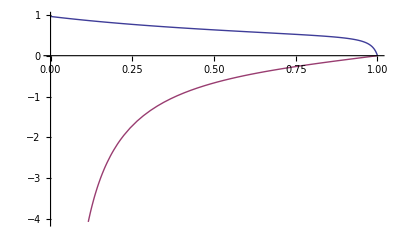

```mathematica
Plot[{(m^2-me^2-m^2 x+me^2 x)/(m^2-m^2 x^2+me^2 x^2)/.m->1/.me->0.2,(1-x)/((-2+x) x)},{x,0,1}]
```

```mathematica
Solve[(-1+x-2 x y+x^2 y)==0,y]
```

{{y→(1-x)/((-2+x) x)}}

```mathematica
Integrate[ y /(-1+x-2 x y+x^2 y),{x,0,1},{y,0,1}]
```

1/4 (2-√5 ArcCsch[2]-√5 ArcSinh[2])

```mathematica
Series[(y (-1+x-2 x y+x^2 y))^(-1-ep),{ep,0,2}]
```

1/(y (-1+x-2 x y+x^2 y))-(Log[y (-1+x-2 x y+x^2 y)] ep)/(y (-1+x-2 x y+x^2 y))+(Log[y (-1+x-2 x y+x^2 y)]^2 ep^2)/(2 y (-1+x-2 x y+x^2 y))+O[ep]^3

```mathematica
Integrate[y/(y (-1+x-2 x y+x^2 y)),{y,0,1},{x,0,1}]
```

1/8 (-π^2+ArcSinh[2] Log[9-4 √5]-4 PolyLog[2,2-√5]+4 PolyLog[2,-2+√5])